```mathematica
Length[Con1]
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,Length[Con1]-3,Length[Con1]}]
```

```mathematica
MSN1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]},{i,1,Length[Con1]}];
```

```mathematica
FindFit[MS1, Sqrt[x/(4 Pi)]+ a1/x^a2 ,{a1,a2},x]
```

```mathematica
{a1->0.014956783680758215,a2->0.16081197973238245}
```

{a1→0.0149568,a2→0.160812}

```mathematica
Sqrt[x/(4 *Pi)]+ a1/x^a2/.%
```

```mathematica
Ms1=0.014956783680758215/x^0.16081197973238245+(√x)/(2 √π)
```

0.0149568/x^0.160812+(√x)/(2 √π)

```mathematica
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,Length[Con1]}];
```

```mathematica
FindFit[MS1,a0 + a1 x^a2 ,{a0,a1,a2},x]
```

{a0→0.023501,a1→0.274575,a2→0.517725}

```mathematica
MMSS1=a0 + a1 x^a2/.%
```

```mathematica
MMSS1=0.023501+0.2745748031661924 x^0.5177245713714081
```

0.023501+0.274575 x^0.517725

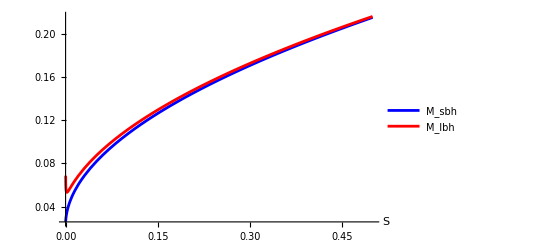

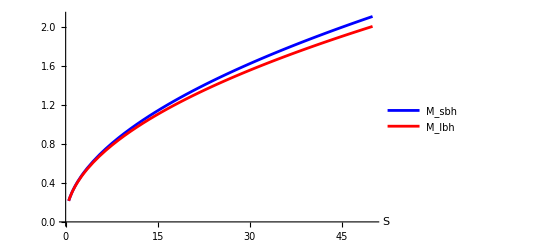

```mathematica
MMSS1plot1=Plot[{MMSS1,Ms1},{x,0.0001,0.5},PlotStyle->{Blue,Red},PlotLegends->Placed[{"M_sbh","M_lbh"},{0.2,0.9}],AxesLabel->{"S"," ",FontSize->28},ImageSize->400]
MMSS1plot2=Plot[{MMSS1,Ms1},{x,0.5,50},PlotStyle->{Blue,Red},PlotLegends->Placed[{"M_sbh","M_lbh"},{0.2,0.9}],AxesOrigin->{0,0},AxesLabel->{"S"," ",FontSize->28},ImageSize->400]
```

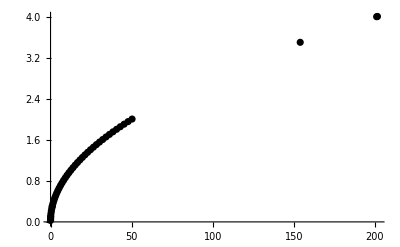

```mathematica
MS11plot=ListPlot[MSN1,PlotStyle->Black,PlotRange->All,ImageSize->400]
```

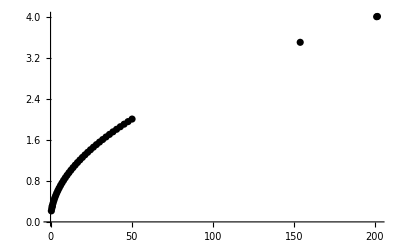

```mathematica
MS12=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,7,Length[Con1]}];
MS12plot=ListPlot[MS12,PlotStyle->Black,PlotRange->All,ImageSize->400]
```

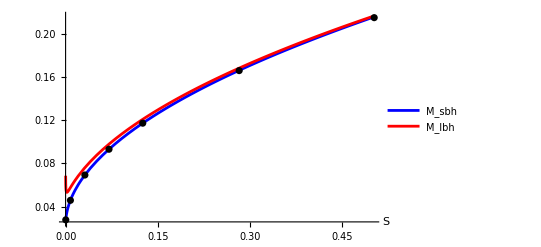

```mathematica
Show[MMSS1plot1,MS11plot]
```

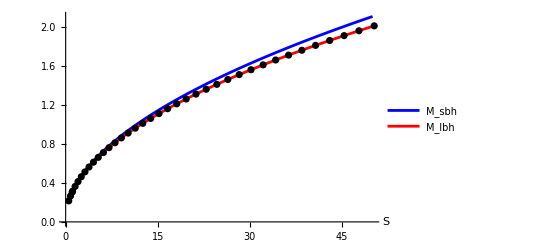

```mathematica
Show[MMSS1plot2,MS12plot]
```